```mathematica
GetDateList[t_] := Module[{nameString, timeFile, timeTable, timeObjectTable},
nameString = "hopperlogs\\tim\\tim" <> ToString[t] <>".txt";
timeFile = Import[nameString, "Table"];
timeTable=Table[
{Join[{2016},timeFile⟦i,{1,2,3,4,5}⟧],
timeFile⟦i,6⟧},
{i,Length[timeFile]}];
timeObjectTable = Table[{DateObject[timeTable⟦i,1⟧],timeTable⟦i,2⟧},{i,Length[timeTable]}];
Return[timeObjectTable]
]
```

{6000,0.183}

{6000,4.29999}

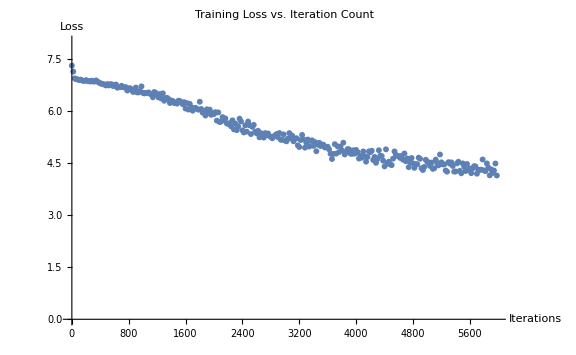

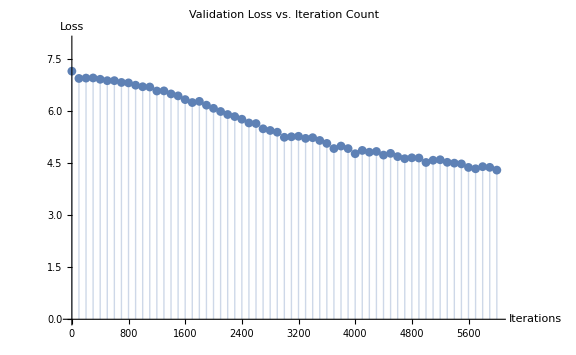

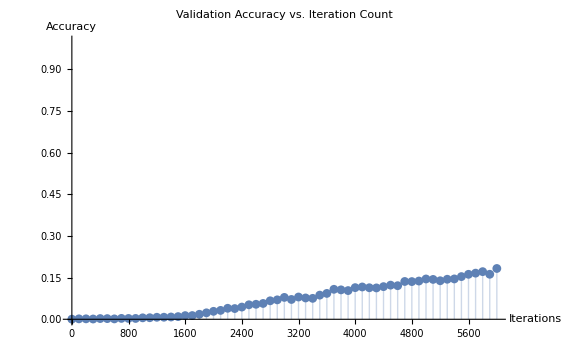

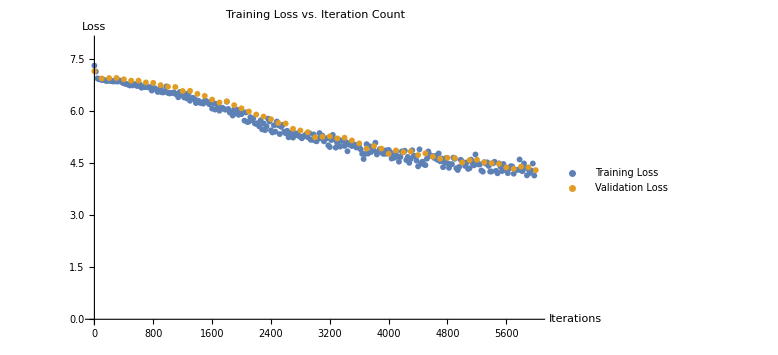

graphs\tlossGraph27.bmp

graphs\vlossGraph27.bmp

graphs\vaccGraph27.bmp

graphs\lossImpGraph27.bmp

```mathematica
FileNum =27;

SetDirectory[NotebookDirectory[]];
nameString = "hopperlogs\\trn\\trn" <> ToString[FileNum] <>".txt";
trainingLoss = Import[nameString, "Table"];
nameString = "hopperlogs\\val\\val" <> ToString[FileNum] <>".txt";
validationLoss = Import[nameString, "Table"];
vacc =validationLoss⟦Range[1,Length[validationLoss],2]⟧;
vloss =validationLoss⟦Range[2,Length[validationLoss]+1,2]⟧;
itrStep = 100; (* Interval between test net instantiations *)
iterRange = Union[Range[0,trainingLoss⟦-1,1⟧,100],{Range[0,trainingLoss⟦-1,1⟧,100]⟦-1⟧+100}];
vaccTable = Table[{iterRange⟦i⟧,vacc⟦i,1⟧},{i,1,Length[vacc]}];
vlossTable = Table[{iterRange⟦i⟧,vloss⟦i,1⟧},{i,1,Length[vloss]}];

vaccTable⟦-1⟧
vlossTable⟦-1⟧

tlossGraph=ListPlot[trainingLoss,PlotLabel->"Training Loss vs. Iteration Count",AxesLabel->{"Iterations","Loss"},PlotRange->8, 
AxesStyle->Thick,BaseStyle->{FontSize->16,FontWeight->Bold, FontColor->Black},ImageSize->Large]
vlossGraph=ListPlot[vlossTable,PlotLabel->"Validation Loss vs. Iteration Count",AxesLabel->{"Iterations","Loss"},Filling->Axis, PlotRange->8, 
AxesStyle->Thick,BaseStyle->{FontSize->16,FontWeight->Bold, FontColor->Black}, ImageSize->Large]
vaccGraph=ListPlot[vaccTable,PlotLabel->"Validation Accuracy vs. Iteration Count",AxesLabel->{"Iterations","Accuracy"},Filling->Axis, PlotRange->1, AxesStyle->Thick,BaseStyle->{FontSize->16,FontWeight->Bold, FontColor->Black},ImageSize->Large]
lossImpGraph=ListPlot[{trainingLoss,vlossTable},PlotLabel->"Training Loss vs. Iteration Count",AxesLabel->{"Iterations","Loss"},PlotRange->8, PlotLegends->{"Training Loss","Validation Loss"}, 
AxesStyle->Thick,BaseStyle->{FontSize->16,FontWeight->Bold, FontColor->Black},ImageSize->Large]

Export["graphs\\tlossGraph" <> ToString[FileNum] <>".bmp",tlossGraph]
Export["graphs\\vlossGraph" <> ToString[FileNum] <>".bmp",vlossGraph]
Export["graphs\\vaccGraph" <> ToString[FileNum] <>".bmp",vaccGraph]
Export["graphs\\lossImpGraph" <> ToString[FileNum] <>".bmp",lossImpGraph]
```

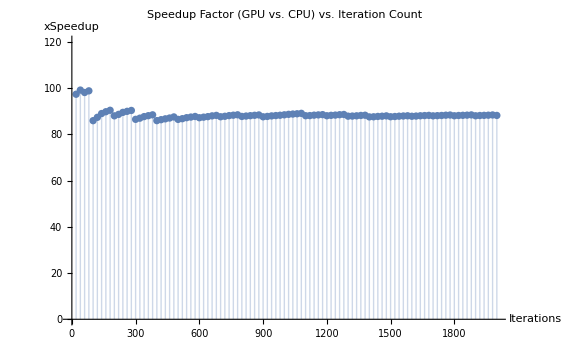

88.4034

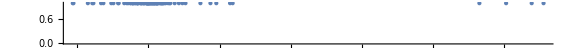

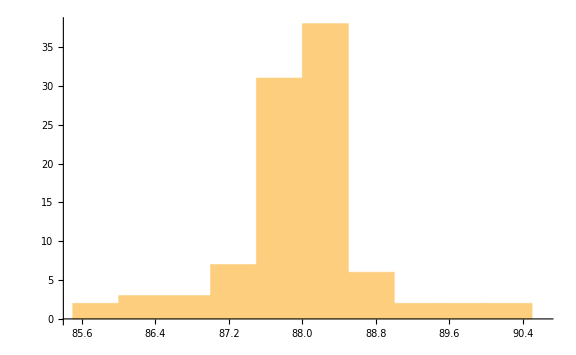

graphs\speedupGraph11-12.bmp

```mathematica
timeFileNum =11;
cpuDates=GetDateList[timeFileNum];
gpuDates=GetDateList[timeFileNum+1];
cpuRef =Table[{DateDifference[cpuDates⟦1,1⟧,cpuDates⟦i,1⟧,"Minute"],cpuDates⟦i,2⟧},{i,Length[cpuDates]}];
gpuRef = Table[{DateDifference[gpuDates⟦1,1⟧,gpuDates⟦i,1⟧,"Minute"],gpuDates⟦i,2⟧},{i,Length[cpuDates]}];
speedup =Table[{gpuDates⟦i,2⟧,(cpuRef⟦i,1⟧/gpuRef⟦i,1⟧)},{i,2,Length[cpuDates]}];
speedupGraph=ListPlot[speedup,PlotLabel->"Speedup Factor (GPU vs. CPU) vs. Iteration Count",AxesLabel->{"Iterations","xSpeedup"},AxesStyle->Thick,BaseStyle->{FontSize->16,FontWeight->Bold, FontColor->Black},
Filling->Axis, PlotRange->120, ImageSize->Large]

speedupVals = Table[(cpuRef⟦i,1⟧/gpuRef⟦i,1⟧),{i,2,Length[cpuDates]}];
Total[speedupVals]/Length[speedupVals]
NumberLinePlot[speedupVals, AxesStyle->Thick,BaseStyle->{FontSize->16,FontWeight->Bold, FontColor->Black},ImageSize->Large]
Histogram[speedupVals, AxesStyle->Thick,BaseStyle->{FontSize->16,FontWeight->Bold, FontColor->Black},ImageSize->Large]


Export["graphs\\speedupGraph" <> ToString[timeFileNum] <> "-" <> ToString[timeFileNum+1] <>".bmp",speedupGraph]
```

```mathematica
timeFileNum = 27;
gpuDates=GetDateList[timeFileNum];
DateDifference[gpuDates⟦1,1⟧,gpuDates⟦Length[gpuDates],1⟧,"Hour"]
```

1.90806 h